```mathematica
Clear[ϵ];
assum={x1∈Reals,x2∈Reals,x3∈Reals,y1∈Reals,y2∈Reals,y3∈Reals,x1^2+x2^2+x3^2==1,y1^2+y2^2+y3^2==1};
(*assum={x1∈Reals,x2∈Reals,x3∈Reals,y1∈Reals,y2∈Reals,y3∈Reals};*)
replace = ⅇ^(2 (-1+x1 y1+x2 y2+x3 y3) ϵ^2);
(*replace = ep[x1,x2,x3,y1,y2,y3];*)
r[x1_,x2_,x3_,y1_,y2_,y3_]=Sqrt[(x1-y1)^2+(x2-y2)^2+(x3-y3)^2];
ep[x1_,x2_,x3_,y1_,y2_,y3_]=FullSimplify[E^(-(ϵ r[x1,x2,x3,y1,y2,y3])^2)];(*Don't plug in the assumptions here, since everyone else has to use it later!*)
FullSimplify[ep[x1,x2,x3,y1,y2,y3],assum]/.{replace->A}
FullSimplify[D[ep[x1,x2,x3,y1,y2,y3],x1],assum]/.{replace->A}
FullSimplify[D[ep[x1,x2,x3,y1,y2,y3],x2],assum]/.{replace->A}
FullSimplify[D[ep[x1,x2,x3,y1,y2,y3],x3],assum]/.{replace->A}
FullSimplify[D[ep[x1,x2,x3,y1,y2,y3],x1,x2],assum]/.{replace->A}
FullSimplify[D[ep[x1,x2,x3,y1,y2,y3],x1,x3],assum]/.{replace->A}
FullSimplify[D[ep[x1,x2,x3,y1,y2,y3],x2,x3],assum]/.{replace->A}
FullSimplify[D[ep[x1,x2,x3,y1,y2,y3],{x1,2}],assum]/.{replace->A}
FullSimplify[D[ep[x1,x2,x3,y1,y2,y3],{x2,2}],assum]/.{replace->A}
FullSimplify[D[ep[x1,x2,x3,y1,y2,y3],{x3,2}],assum]/.{replace->A}
```

ⅇ^(2 (-1+x1 y1+x2 y2+x3 y3) ϵ^2)

-2 ⅇ^(2 (-1+x1 y1+x2 y2+x3 y3) ϵ^2) (x1-y1) ϵ^2

-2 ⅇ^(2 (-1+x1 y1+x2 y2+x3 y3) ϵ^2) (x2-y2) ϵ^2

-2 ⅇ^(2 (-1+x1 y1+x2 y2+x3 y3) ϵ^2) (x3-y3) ϵ^2

4 ⅇ^(2 (-1+x1 y1+x2 y2+x3 y3) ϵ^2) (x1-y1) (x2-y2) ϵ^4

4 ⅇ^(2 (-1+x1 y1+x2 y2+x3 y3) ϵ^2) (x1-y1) (x3-y3) ϵ^4

4 ⅇ^(2 (-1+x1 y1+x2 y2+x3 y3) ϵ^2) (x2-y2) (x3-y3) ϵ^4

ⅇ^(2 (-1+x1 y1+x2 y2+x3 y3) ϵ^2) (-2 ϵ^2+4 (x1-y1)^2 ϵ^4)

ⅇ^(2 (-1+x1 y1+x2 y2+x3 y3) ϵ^2) (-2 ϵ^2+4 (x2-y2)^2 ϵ^4)

ⅇ^(2 (-1+x1 y1+x2 y2+x3 y3) ϵ^2) (-2 ϵ^2+4 (x3-y3)^2 ϵ^4)

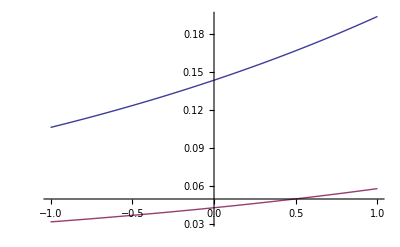

```mathematica
ϵ=1.0;
Plot[{ep[x,0.1,0.1,0.15,0.15,0.15],epx[x,0.1,0.1,0.15,0.15,0.15]},{x,-1,1}]
```

```mathematica
Solve[3x^2==1.0,x]
```

{{x→-0.57735},{x→0.57735}}

## Deriving the matrix-valued RBF

We’d like to substitute a matrix-valued RBF for u.

```mathematica
vars={x,y,z};
ϕofr=ϕ[r[x,y,z]];
ϕd=Table[FullSimplify[D[ ϕofr, vars[[i]]],assums],{i,1,3}];
ϕdd=Table[FullSimplify[D[ ϕd[[i]], vars[[j]]],assums],{i,1,3},{j,1,3}]/.{x->x1,y->x2,z->x3};
H[x1_,x2_,x3_]=ϕdd;
Hdx[x1_,x2_,x3_]=D[H[x,y,z],x]/.{x->x1,y->x2,z->x3};
Hdy[x1_,x2_,x3_]=D[H[x,y,z],y]/.{x->x1,y->x2,z->x3};
Hdz[x1_,x2_,x3_]=D[H[x,y,z],z]/.{x->x1,y->x2,z->x3};
Hdxx[x1_,x2_,x3_]=D[Hdx[x,y,z],x]/.{x->x1,y->x2,z->x3};
Hdyy[x1_,x2_,x3_]=D[Hdy[x,y,z],y]/.{x->x1,y->x2,z->x3};
Hdzz[x1_,x2_,x3_]=D[Hdz[x,y,z],z]/.{x->x1,y->x2,z->x3};
Hdxy[x1_,x2_,x3_]=D[Hdx[x,y,z],y]/.{x->x1,y->x2,z->x3};
Hdyz[x1_,x2_,x3_]=D[Hdy[x,y,z],z]/.{x->x1,y->x2,z->x3};
Hdxz[x1_,x2_,x3_]=D[Hdx[x,y,z],z]/.{x->x1,y->x2,z->x3};
```

```mathematica
Q[x_,y_,z_]={
{0,-z,y},
{z,0,-x},
{-y,x,0}};
P[x_,y_,z_]=IdentityMatrix[3]-{{x},{y},{z}}.{{x,y,z}};
```

```mathematica
Ψdiv[x1_,x2_,x3_,y1_,y2_,y3_]=FullSimplify[Transpose[Q[x1,x2,x3]].-H[x1-y1,x2-y2,x3-y3].Q[y1,y2,y3],assum];
```

```mathematica
Ψdiv[x1,y1,z1,x2,y2,z2][[1,;;]]//TableForm
```

-ϕ''[r[x1-x2,y1-y2,z1-z2]] (y1 r^(0,0,1)[x1-x2,y1-y2,z1-z2]-z1 r^(0,1,0)[x1-x2,y1-y2,z1-z2]) (y2 r^(0,0,1)[x1-x2,y1-y2,z1-z2]-z2 r^(0,1,0)[x1-x2,y1-y2,z1-z2])+ϕ'[r[x1-x2,y1-y2,z1-z2]] (-y1 y2 r^(0,0,2)[x1-x2,y1-y2,z1-z2]+(y2 z1+y1 z2) r^(0,1,1)[x1-x2,y1-y2,z1-z2]-z1 z2 r^(0,2,0)[x1-x2,y1-y2,z1-z2])
ϕ''[r[x1-x2,y1-y2,z1-z2]] (y1 r^(0,0,1)[x1-x2,y1-y2,z1-z2]-z1 r^(0,1,0)[x1-x2,y1-y2,z1-z2]) (x2 r^(0,0,1)[x1-x2,y1-y2,z1-z2]-z2 r^(1,0,0)[x1-x2,y1-y2,z1-z2])+ϕ'[r[x1-x2,y1-y2,z1-z2]] (x2 y1 r^(0,0,2)[x1-x2,y1-y2,z1-z2]-x2 z1 r^(0,1,1)[x1-x2,y1-y2,z1-z2]-y1 z2 r^(1,0,1)[x1-x2,y1-y2,z1-z2]+z1 z2 r^(1,1,0)[x1-x2,y1-y2,z1-z2])
-ϕ''[r[x1-x2,y1-y2,z1-z2]] (y1 r^(0,0,1)[x1-x2,y1-y2,z1-z2]-z1 r^(0,1,0)[x1-x2,y1-y2,z1-z2]) (x2 r^(0,1,0)[x1-x2,y1-y2,z1-z2]-y2 r^(1,0,0)[x1-x2,y1-y2,z1-z2])+ϕ'[r[x1-x2,y1-y2,z1-z2]] (-x2 y1 r^(0,1,1)[x1-x2,y1-y2,z1-z2]+x2 z1 r^(0,2,0)[x1-x2,y1-y2,z1-z2]+y1 y2 r^(1,0,1)[x1-x2,y1-y2,z1-z2]-y2 z1 r^(1,1,0)[x1-x2,y1-y2,z1-z2])